# PDEs

Partial Differential Equations (PDEs) are the source of most (but far from all) large scale linear algebra problems. We are going to discretize one standard PDE with a few techniques.

## Laplacian -Δu=f

This means in 2D Cartesian coordinates (x, y) that we are trying to find a function satisfying
	-Δu=-(u_xx+u_yy)=f(x,y)
on some domain Ω⊂ℝ^2 with suitable boundary conditions on the boundary ∂Ω.  The simplest conditions are Dirichlet conditions 
	u(x,y)=u_0(x,y)  for {x,y}∈∂Ω. 
Other boundary conditions are common. Dirichlet is easiest to understand.

This means in 1D Cartesian coordinates x our Dirichlet problem is to find a function satisfying 
	-u_xx=f 
on an interval a<x<b with u(a) and u(b) specified.  We are going to do the 1D problem first.

### 1D: Centered Finite Differences

We are going to approximate the solution for
	-u_xx=f(x^2)   for x∈(0,1) and u(0)=α and u(1)=3β
by splitting the interval up into equally spaced subintervals.  Define
	Δx=1/(n+1) and x_i=i Δx for i=0,…,n
so that the end points are x_0=0  and x_(n+1)=1.  Approximate the second derivative using the standard second difference
	u_xx(x_i)=(u(x_(i-1))-2 u(x_i)+u(x_(i+1)))/Δx^2
and substitute into the equation at the interior points and multiply by -Δx^2 to get 
	u(x_(i-1))-2 u(x_i)+u(x_(i+1)) | = | -Δx^2f(x_i) for i=1:n
while the boundary conditions give 
	u(x_0)=α and u(x_(n+1))=β.
The solution of the linear system 
	-2 u_1 | + | u_2 | + |   |   |   |   |   |   | = | -Δx^2f(x_1) | - | α
u_1 | - | 2 u_2 | + | u_3 |   |   |   |   |   | = | -Δx^2f(x_2) |   |  
  |   | u_2 | + | -2 u_3 | + | u_4 |   |   |   | = | -Δx^2f(x_3) |   |  
  |   |   |   |   | ⋱ |   |   |   |   | ⋮ | ⋮ |   |  
  |   |   |   |   | u_(n-2) | + | -2 u_(n-1) | + | u_n | = | -Δx^2f(x_(n-1)) |   |  
  |   |   |   |   |   |   | u_(n-1) | + | -2 u_n | = | -Δx^2f(x_(n-1)) | - | β
gives an approximation u_i≈u(x_i).  The approximation gets better as Δx gets smaller or equivalently n gets bigger.  Hopefully this is obviously the solution of the linear system
	A.u=b
where A is the symmetric tridiagonal matrix with -2 on the diagonal and 1 on the off diagonals.

```mathematica
uSol[x_]:=x Cos[x]-x^3;
{α,β}={uSol[0],uSol[1]};
f[x_]=-D[uSol[x],{x,2}];
m=12; Δx=1.0/(m+1);
A=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{m,m}];
b=-Δx^2 Table[f[i Δx],{i,1,m}];b⟦{1,m}⟧-={α,β};
u=LinearSolve[A,b]; uBC=Join[{α},u,{β}];
TabView[{
"Sol"->Show[
Plot[ uSol[x],{x,0,1},PlotStyle->Red],
ListPlot[uBC,DataRange->{0,1}],
PlotLabel->m
],
"Error"->ListPlot[u-Table[uSol[i Δx],{i,m}],PlotLabel->m]
}]
```

12

It is more complicated to do this in 2D because numbering the approximation points is less simple.

### 2D: Centered Finite Differences

It is straight forward to extend this argument to a square Ω=(0,1)×(0,1)⊂ℝ^2 with n points in each direction! Define 
	h=1/(n+1)
	p_(i,j)=h{i,j}
The equivalent approximation schemes are 
	u_xx(p_(i,j))≈(u(p_(i-1,j))-2u(p_(i,j))+u(p_(i+1,j)))/h^2
and  
	u_yy(p_(i,j))≈(u(p_(i,j-1))-2u(p_(i,j))+u(p_(i,j+1)))/h^2.
The approximation for -Δ you get by summing these two is frequently presented as the “stencil”
	0 |     1 | 0
1 | -4 | 1
0 |     1 | 0
Our equations are relatively simple again
	-4 u_(i,j)+u_(i-1,j)+u_(i+1,j)+u_(i,j-1)+u_(i,j+1)==-h^2f(p_(i,j))  for i=1:n and j=1:n
The boundary conditions now look like
	u_(0,j)=u(p_(0,j)) and u_(m+1,j)=u(p_(m+1,j))  for j=0:n
and 
	u_(i,0)=u(p_(i,0)) and u_(i,m+1)=u(p_(i,m+1))for i=0:n.
This is harder to implement than the 1D version!  It is largely bookkeeping but it is important bookkeeping.  As we will see different PDE packages deal with the bookkeeping in different ways

```mathematica
Clear[uSol,x,y,p]
uSol[{x_,y_}]:=x Cos[x y]-x^3+Sin[y]Cos[Sin[x^2+y]+y];
f[{x_,y_}]=-(D[uSol[{x,y}],{x,2}]+D[uSol[{x,y}],{y,2}]);
n=12; h=1.0/(n+1);
p[i_,j_]:=h{i,j};
m=n^2;
A=SparseArray[{},{m,m}];b=ConstantArray[0,m];
k[i_,j_]:=i+n(j-1)
```

k is just a choice of numbering scheme for the points p_(i,j)!

```mathematica
Table[k[i,j],{i,1,n},{j,1,n}]
```

{{1,13,25,37,49,61,73,85,97,109,121,133},{2,14,26,38,50,62,74,86,98,110,122,134},{3,15,27,39,51,63,75,87,99,111,123,135},{4,16,28,40,52,64,76,88,100,112,124,136},{5,17,29,41,53,65,77,89,101,113,125,137},{6,18,30,42,54,66,78,90,102,114,126,138},{7,19,31,43,55,67,79,91,103,115,127,139},{8,20,32,44,56,68,80,92,104,116,128,140},{9,21,33,45,57,69,81,93,105,117,129,141},{10,22,34,46,58,70,82,94,106,118,130,142},{11,23,35,47,59,71,83,95,107,119,131,143},{12,24,36,48,60,72,84,96,108,120,132,144}}

It is fairly easy to put all the RHS function values from f[x,y] into the RHS vector b. The boundary condition terms are trickier.

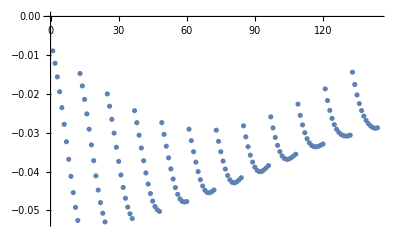

```mathematica
Do[b⟦k[i,j]⟧=-h^2 f[p[i,j]],{i,n},{j,n}];
ListPlot[b]
```

It is fairly easy to put the matrix entries into the correct places.

```mathematica
A=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{n^2,n^2}];
b=ConstantArray[0,n^2];
b=-Δx^2 Table[f[i Δx],{i,1,m}];b⟦{1,m}⟧-={α,β};
u=LinearSolve[A,b]; uBC=Join[{α},u,{β}];
TabView[{
"Sol"->Show[
Plot[ uSol[x],{x,0,1},PlotStyle->Red],
ListPlot[uBC,DataRange->{0,1}],
PlotLabel->m
],
"Error"->ListPlot[u-Table[uSol[i Δx],{i,m}],PlotLabel->m]
}]
```

12

It is more complicated to do this in 2D because numbering the approximation points is less simple.